```mathematica
ex1dot2dot[n_]:=Factorial[n]/Factorial[n-1]
```

```mathematica
m=5
ex1dot2dot[m]
```

```mathematica
(*Pascal's Formula. 
Returns an array of numbers corresponding to the terms of the nth level of Pascal's Triangle.
EG:


Table[Factorial[(n-1)]/(Factorial[k]*Factorial[(n-1-k)])+Factorial[(n-1)]/(Factorial[(k-1)]*Factorial[n-k]),{n,1,10},{k,0,10}]

{{1,1,0,0,0,0,0,0,0,0,0},{1,2,1,0,0,0,0,0,0,0,0},{1,3,3,1,0,0,0,0,0,0,0},{1,4,6,4,1,0,0,0,0,0,0},{1,5,10,10,5,1,0,0,0,0,0},{1,6,15,20,15,6,1,0,0,0,0},{1,7,21,35,35,21,7,1,0,0,0},{1,8,28,56,70,56,28,8,1,0,0},{1,9,36,84,126,126,84,36,9,1,0},{1,10,45,120,210,252,210,120,45,10,1}}

*)
Foo:=Table[Factorial[(n-1)]/(Factorial[k]*Factorial[(n-1-k)])+Factorial[(n-1)]/(Factorial[(k-1)]*Factorial[n-k]),{n,1,10},{k,0,10}]
```

```mathematica
Table[ex1dot2dot[n],{n,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
BarChart[Foo[[10]]]
```

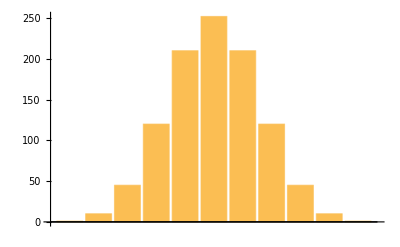

```mathematica
\

2*ArcCos[Sqrt[22]/(Sqrt[72]/2)]
```

2 ArcCos[(√11)/3]

```mathematica
2*ArcCos[(√11)/3]
```

2 ArcCos[(√11)/3]

```mathematica
N[ 2*ArcCos[(√11)/3],4]
```

0.911 ⅈ

```mathematica
0.9851107833377456596`4.*57.2958
```

56.4427